# Implementation of semiconductor Bloch equation in topological materials: ultrafast dynamics driven by THz lasers in Chern insulators Alexis Chacon

## Semiconductor Bloch Equations (SBEs) to describe the laser-topological-material interaction in the Length Gauge (LG)

(1)     ∂_t π(k⃗,t) - E⃗(t) ·∇ π(k⃗,t)  = -ⅈ[ϵ_g(  k⃗ )   + (ξ⃗)_g(k⃗) · E⃗(t)  - ⅈ/T2]  π(k⃗,t)   -  ⅈ  (d⃗)_cv(k⃗)  ·  E⃗(t);      Evolution of the coherence,  π(k⃗,t)
     (2)     ∂_t n_c(k⃗,t) - E⃗(t) ·∇ n_c(k⃗,t)  = -2 Im[    Conjugate[ (d⃗)_cv(k⃗)  ]  ·  E⃗(t)  π(k⃗,t) ];                         Evolution of the Occupation, conduction band, nc
     (3)     ∂_t n_v(k⃗,t) - E⃗(t) ·∇ n_v(k⃗,t)  = +2 Im[    Conjugate[ (d⃗)_cv(k⃗)  ]  ·  E⃗(t)  π(k⃗,t) ];                   Evolution of the Occup. of the valence band, nv
       
 Constrain,
        nc(k⃗,t)  + nv(k⃗,t)  =1

## Cleaning notebook variables and setting paths

```mathematica
ClearAll["Global`*"] ;

Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];

$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`26"&);

rootPathA=NotebookDirectory[]
toFixedWidth[n_Integer,width_Integer]:=StringJoin[PadLeft[Characters[ToString[n]],width,"0"]];
toNumberedFileName[fname_,n_Integer]:=ToString@StringForm[fname<>toFixedWidth[n,5]];

efac=27.2;
aufac=0.5;
NotebookDirectory[];
AbsoluteTime[];
```

/Users/achacon/Documents/Workplace/MichaelC/TopologyProj/CodeDeveloping/SF/Mathematica2/

0.5

## Testing open and reading binary files

```mathematica
qindex0 = 0;
fname0 = toNumberedFileName["BinaryTest",0];
fname0 = toNumberedFileName[fname0<>"_kyIndex_",qindex0];

testList ={-1.01,0,1,2.0001};
file=  rootPathA <> fname0 <> ".bin";
BinaryWrite[file,testList,"Real64"];
BinaryReadList[file,"Real64"];

Close[file];
Sin2:=Function[x, Sin[x] ]
Cos2:=Function[x,Cos[x] ]
```

## Laser field

```mathematica
Af0 :=Function[t, 

(*e0/w0 (Cos[w0 t] Exp[-.5(t/alpha0)^2] -  Cos[w0 tmin0]  Exp[-.5(tmin0/alpha0)^2])*)


(e0 (Cos[t w0] (-1+Ncycles^2+Ncycles^2 Cos[(t w0)/Ncycles])+Ncycles Sin[t w0] Sin[(t w0)/Ncycles]))/(2 (-1+Ncycles) (1+Ncycles) w0)


];

Af :=Function[t, 

(*e0/w0 (Cos[w0 t] Exp[-.5(t/alpha0)^2] -  Cos[w0 tmin0]  Exp[-.5(tmin0/alpha0)^2])*)

If[Abs[t]≤ CosWidth/2.,

Af0[t]-Af0[CosWidth/2.]
,
0.
]

];


gEf:= Function[t, - D[Af[ta],ta]/.ta-> t     ];

Ef := Function[t,
(*gEf[t]-gEf[tmin0] *)

If[Abs[t]≤ CosWidth/2.,

e0 Cos[w0 t/Ncycles/2]Cos[w0 t/Ncycles/2] Sin[w0 t]
,

0.
]


];


(* TIME AND FREQUENCY AXIS  *)


timeaxes := Function[
{dt,Nt},
tmax= dt*(Nt-1)/2.;
wmax=Pi/dt;
dw = 2 Pi/Nt/dt;
{Table[tmin0 + i dt,{i,0,Nt-1}]
,Table[-wmax + i dw,{i,0,Nt-1}]
}
];
```

## Haldane Model (HM) and topological Chern insulators Hamiltonian and its “components” B0, B1,... H(k) = B0*sig0 + B1*sig1 + B2*sig2 + B3*sig3 where, sig1, sig2, sig3 are Pauli’s matrices, sig0 identity matrix

```mathematica
B0 := Function[
{kx,ky}
,2 t2 Cos[ϕ]*
Sum[ 

tempB0= kx *bx[[i]] +ky *by[[i]];

Cos2[tempB0  ] 

,{i,1,3}
] 
];


B1:= Function[
{kx,ky}
, t1 *
Sum[ 
tempB1=kx *ax[[i]] +ky *ay[[i]];
Cos2[ tempB1 ]

,{i,1,3}

]
];


B2:= Function[
{kx,ky} 
, t1 Sum[
 tempB2=kx *ax[[i]] +ky *ay[[i]];
Sin2[ tempB2 ]
,{i,1,3}
]
];


B3 := Function[ 
{kx,ky}
,M-2 t2*Sin[ϕ]Sum[ 
tempB3=kx *bx[[i]] +ky *by[[i]];
Sin2[ tempB3 ]
,{i,1,3} 

] 
];



BNorm:=Function[
{kx,ky}
, Sqrt[ 
B1[kx,ky]^2 +B2[kx,ky]^2+B3[kx,ky]^2
 ]
];


(*Definition of quantize indexes/axes*)
nB1:=Function[
{kx,ky}
, B1[kx,ky]/BNorm[kx,ky] 
];


nB2:=Function[
{kx,ky}
,B2[kx,ky]/BNorm[kx,ky] 
];


nB3:=Function[
{kx,ky}
, B3[kx,ky]/BNorm[kx,ky] 
];

Phi:=Function[{kx,ky},ArcTan[B2[kx,ky]/B1[kx,ky]] //Simplify];
Theta := Function[{kx,ky},ArcCos[nB3[kx,ky]] ];
```

## Invariant easy quantities

```mathematica
(*Definition of Energy dispersion for conduction and valance band*)
Ec:=Function[{kx,ky}
, 
B0[kx,ky]  + BNorm[kx,ky]

];



Ev:=Function[{kx,ky}
, B0[kx,ky]  - BNorm[kx,ky]
];



(*Group velocities of the conduction and valance band*)
cGroupVel := Function[{kx,ky}
,Grad[Ec[kkx,kky]
,{kkx,kky}]/.kkx-> kx/.kky->ky
];



vGroupVel := Function[{kx,ky},
Grad[Ev[kkx,kky]
,{kkx,kky}]/.kkx-> kx/.kky->ky
];



(*Energy Gap, Eg = Ec- Ev and Berry Connection 'Chig' Gap*)
 Eg := Function[
{kx,ky}
, Ec[kx,ky] 
- Ev[kx,ky] 
];


(*Functions to rotate axis*)
QuantizationAxis:=Function[{kx,ky},
gauge (*Return vector {1,0,0}*)
]


(*ROTATEING FUNCTION ALONG DIFFERNT SPIN-AXIS "PAULI MATRIXES"*)
RotateOnBAt0:=

Function[{kx,ky},
Module[
{
n3p,n2p,n1p,

nBVecAtK = 
{
    nB1[kx,ky]
,nB2[kx,ky]
,nB3[kx,ky]
},

nB3p,nB2p,nB1p, orthoVecs

},

n3p =QuantizationAxis[kx,ky] ;
orthoVecs =
 Orthogonalize[
{
n3p
,RotateLeft[n3p,1]
,RotateLeft[n3p,2]
}
];

n1p = orthoVecs[[3]];
n2p = orthoVecs[[2]];

nB3p = nBVecAtK.n3p;
nB2p = nBVecAtK.n2p;
nB1p = nBVecAtK.n1p;

{nB1p,nB2p,nB3p}
]
];


RotateUNOnBAt0:=Function[
{kx,ky},

Module[{
n3p,n2p,n1p,orthoVecs,
bVecAtK = 
{
     B1[kx,ky]
, B2[kx,ky]
, B3[kx,ky]
},
b3p,b2p,b1p
},

n3p =QuantizationAxis[kx,ky] ;

orthoVecs = Orthogonalize[
{
n3p
,RotateLeft[n3p,1]
,RotateLeft[n3p,2]
}

];

n1p = orthoVecs[[3]];
n2p = orthoVecs[[2]];

b3p = bVecAtK.n3p;
b2p = bVecAtK.n2p;
b1p = bVecAtK.n1p;

{b1p,b2p,b3p}
]

];
```

## New connections and Berry features

```mathematica
(*singular points at gauge (1,0,0)*)

ks00 ={-1.7,0};
ks01 ={-1.7+2 kxMax,0};

ks10 ={0.8,1.45};
ks11 ={0.8-2 kxMax,1.45};
ks12 ={0.8,-1.45};
ks13 ={0.8-2 kxMax,-1.45};

ks20 ={-1.1,1.85};
ks21 ={-1.1+2 kxMax,1.85};
ks22 ={-1.1,-1.85};
ks23 ={-1.1+2 kxMax,-1.85};


MyRegularization := Function[{kx,ky,ks},

reg0 Exp[-((ky-ks[[2]])^2+(kx-ks[[1]])^2)/width]

]

QuantizationAxis:=Function[
{kx,ky},
gauge
]


Hamilton:= Function[{kx,ky},
Module[
{

B0p = B0[kx,ky],
B1p=RotateUNOnBAt0[kx,ky][[1]],
B2p =RotateUNOnBAt0[kx,ky][[2]],
B3p =RotateUNOnBAt0[kx,ky][[3]]

(*,B1p=B1[kx,ky]
,B2p =B2[kx,ky]
,B3p =B3[kx,ky]
*)

(*B1p=RotateUNOnBAt0[kx,ky][[1]],
B2p =RotateUNOnBAt0[kx,ky][[2]],
B3p =RotateUNOnBAt0[kx,ky][[3]]*)



(***
B1p=B1[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by],
B2p=B2[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by],
B3p=B3[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]
***)

},

B0p IdentityMatrix[2] + B1p PauliMatrix[1] +B2p PauliMatrix[2] + B3p PauliMatrix[3]

]

];

HamiltonGrad := Function[{kx,ky},

Grad[Hamilton[kkx,kky],{kkx,kky}]/.kkx-> kx/.kky-> ky

];


ANorm:= Function[{kx,ky},

Module[
{
B1p=RotateUNOnBAt0[kx,ky][[1]],
B2p =RotateUNOnBAt0[kx,ky][[2]],
B3p =RotateUNOnBAt0[kx,ky][[3]]
},


Sqrt[
  2( B1p^2 +B2p^2+B3p^2) +  
2 BNorm[kx,ky] B3p
]

]


];


uCondNew:=Function[{kx,ky}
,

(*{
Exp[-I*Phi[kx,ky]/2]Cos[Theta[kx,ky]/2]
,Exp[I*Phi[kx,ky]/2]Sin[Theta[kx,ky]/2]
}
*)

Module[
{
B1p =RotateUNOnBAt0[kx,ky][[1]],
B2p =RotateUNOnBAt0[kx,ky][[2]],
B3p =RotateUNOnBAt0[kx,ky][[3]]
},

{
B3p +  BNorm[kx,ky]
,
B1p + I B2p
}/ANorm[kx,ky]
]
];


uValNew:=Function[
{kx,ky}
(*,
{
Exp[-I*Phi[kx,ky]/2]Sin[Theta[kx,ky]/2],
-Exp[I*Phi[kx,ky]/2]Cos[Theta[kx,ky]/2]
}*)
,Module[
{
B1p=RotateUNOnBAt0[kx,ky][[1]],
B2p =RotateUNOnBAt0[kx,ky][[2]],
B3p =RotateUNOnBAt0[kx,ky][[3]]
}
,{
-B1p + I B2p,
+B3p +  BNorm[kx,ky]

}/ANorm[kx,ky]
]
	
];


xcvMomentumMatrixElements:= Function[{kx,ky}, 
Conjugate[uCondNew[kx,ky]].( HamiltonGrad[kx,ky][[All,All,1]] . uValNew [kx,ky])
]


VWaveGrad := Function[

{kx,ky}

,Grad[uValNew[kkx,kky]
,{kkx,kky}]/.kkx-> kx/.kky-> ky


];


CWaveGrad := Function[
{kx,ky}

,Grad[uCondNew[kkx,kky]
,{kkx,kky}]/.kkx-> kx/.kky-> ky

];


(*BERRY CONNECTION FOR THE CONDUCTION BAND*)
cBerryConnection := Function[{kx,ky},

BCon=I Conjugate[uCondNew[kx,ky]]. CWaveGrad[kx,ky];


BCon

];


(*DIPOLE MATRIX ELEMENT BETWEEN THE VALENCE AND CONDUCTION BAND*)
cvDipole := Function[

{kx,ky},

I Conjugate[uCondNew[kx,ky]]. VWaveGrad[kx,ky]

(*If[ky<0,tempDip=-tempDip ];*)

(*tempDip*)

];


vcDipole := Function[
{kx,ky},

I Conjugate[uValNew[kx,ky]]. CWaveGrad[kx,ky]

];

(*BERRY CURVATURE FOR THE CONDUCTION BAND*)
cBerryCurvature:= Function[

{kx,ky},

Re[
I  (
Conjugate[CWaveGrad[kx,ky][[All,1]]].CWaveGrad[kx,ky][[All,2]]
- Conjugate[CWaveGrad[kx,ky][[All,2]]].CWaveGrad[kx,ky][[All,1]]
)
]

];


cBerryCurvaDipole := Function[{kx,ky},
2 Im[ 

Conjugate[cvDipole[kx,ky][[1]] ] cvDipole[kx,ky][[2]]  

]
]



(********************************)
(*Calculation of the CHERN No.*)

CherNo:=
 NIntegrate[cBerryCurvature[kx,ky] (*cBerryCurvaDipole[kx,ky]*),{kx,kxMin,kxMax},{ky,
kyMin, kyMax}  ]/(2 Pi)
```

## Axis and finite difference derivative under periodic boundary conditions

```mathematica
(* Momentum axis *)
momaxis := Function[
{Nk,kmin},

dk=-2kmin/(Nk-1);
Table[kmin + dk i,{i,0,Nk-1}]

]; 

(*Derivative operator*)
FirstDerOperator := Function [
{dx,Nx},

Mtemp=SparseArray[{Band[{1,1}]->0,Band[{2,1}]->-1,Band[{1,2}]->1},{Nx,Nx}]/2/dx;
Mtemp[[1]][[Nx-1]]=1/dx/2.;
Mtemp[[1]][[1]]=-0/dx/2;
Mtemp[[Nx]][[Nx]]=0/dx/2;
Mtemp[[Nx]][[2]]=-1/dx/2.;
Mtemp

];
```

## Vector bases of HM (Hexagonal lattice)

```mathematica
(*Lattice Constant*)
a0=1.0/0.529(*1.0/0.529;*)(**)


(*Next Nearest Neighbor, NNN, vectors of the HoneyComb Lattice*)
b1 = {Sqrt[3],0}*a0;
b2 = {-Sqrt[3]/2,+3/2}*a0;
b3 = {-Sqrt[3]/2,-3/2}*a0;

bx1=b1[[1]];
by1=b1[[2]];

bx2=b2[[1]];
by2=b2[[2]];

bx3=b3[[1]];
by3=b3[[2]];

b = {b1,b2,b3};


(*Nearest Neighbor, NN, vectors of the HoneyComb Lattice*)
a1 = {0,1}*a0;
a2 = {-Sqrt[3]/2,-1/2}*a0;
a3 = {Sqrt[3]/2,-1/2}*a0;

a= {a1,a2,a3};


ax1=a1[[1]];
ay1=a1[[2]];

ax2=a2[[1]];
ay2=a2[[2]];

ax3=a3[[1]];
ay3=a3[[2]];

aax ={ a1[[1]],a2[[1]],a3[[1]] };
aay ={ a1[[2]],a2[[2]],a3[[2]] };

bbx ={ b1[[1]],b2[[1]],b3[[1]] };
bby ={ b1[[2]],b2[[2]],b3[[2]] };

(*Creating momentum axis limits*)
xtemp=    2 N[ Pi/Sqrt[3]/a0];
ytemp=   2 N[ Pi/3/a0];
kxMin= - xtemp ; kxMax=xtemp;
kyMin = - ytemp  ; kyMax=ytemp ; 


(*K' and K points with respect to the gamma points on the BZ*)
K1= {-4 Pi/(3*Sqrt[3] a0),0};
K2 = {4 Pi/(3*Sqrt[3] a0),0};

t1=0.075;
t2=t1/3.;
M=2.54* t2;
phi0=0.00; 

ϕ=phi0;

t01=0.075;
t02=t01/3.;
M0=2.54* t02;

xdir=1;
ydir=2;

size=450;

ax=aax;
ay=aay;
bx=bbx;
by=bby;


gauge={1,0,0};
QuantizationAxis:=Function[
{kx,ky},
gauge
];
```

1.890359168241965973534972

## dipole evaluation and visualization

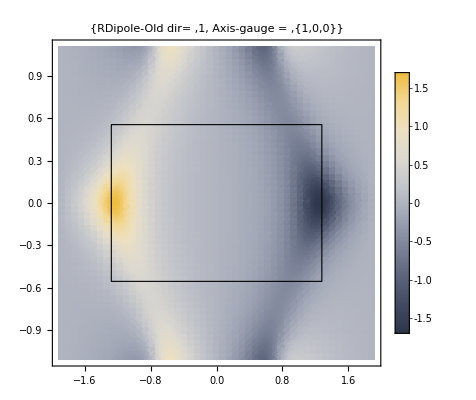
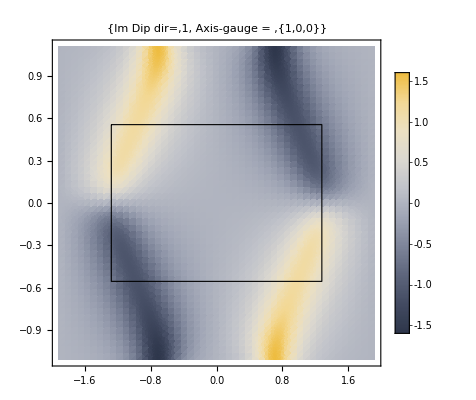

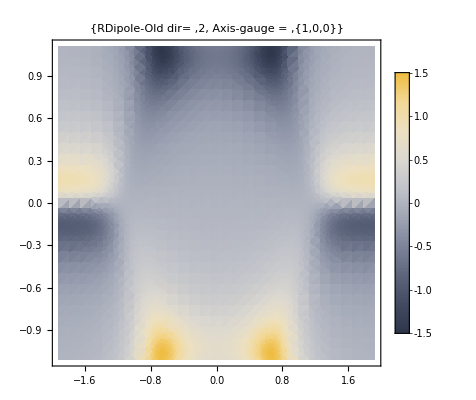
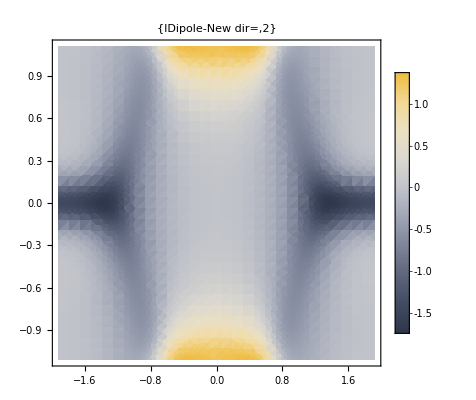

```mathematica
(*gauge={1,0,0};*)

size=400;
width=.1^2;
reg0=.075;

xdir=1;
ydir=2;
eps0=t01/2.;

epilogBZ={EdgeForm@Thick,FaceForm@None,Polygon[Table[{K1[[1]] Cos[2π i/6],K1[[1]]Sin[2π i/6]},{i,0,5}]]};
box={{K1[[1]] ,ytemp/2},{-K1[[1]] ,ytemp/2},{-K1[[1]] ,-ytemp/2},{K1[[1]] ,-ytemp/2}};
epilogBZ={EdgeForm@Thick,FaceForm@None,Polygon[ Table[box[[i]],{i,1,4} ]]};


{
DensityPlot[
Re[cvDipole[kx,ky][[xdir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"RDipole-Old dir= ", xdir," Axis-gauge = ", gauge}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 50
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None
,Epilog->epilogBZ
,TicksStyle->Large ]
,

(*gauge={0,1,0};*)


DensityPlot[
Im[cvDipole[kx,ky][[xdir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"Im Dip dir=" , xdir , " Axis-gauge = ", gauge}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 50
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None 
,Epilog->epilogBZ
,TicksStyle->Large]
};


{
DensityPlot[
Re[cvDipole[kx,ky][[ydir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"RDipole-Old dir= ", ydir," Axis-gauge = ", gauge}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 30
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None
,TicksStyle->Large ]
,
DensityPlot[
Im[cvDipole[kx,ky][[ydir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"IDipole-New dir=" , ydir}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 30
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None
,TicksStyle->Larger ]
};
```

## Dipole phase

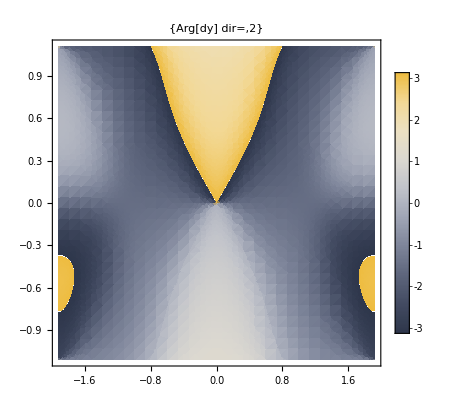

```mathematica
DensityPlot[
Arg[cvDipole[kx,ky][[ydir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"Arg[dy] dir=" , ydir}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 30
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None
,TicksStyle->Larger ]
```

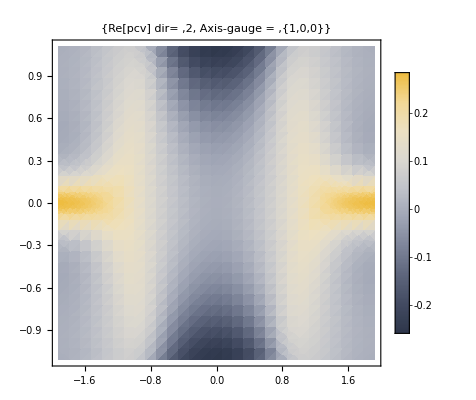
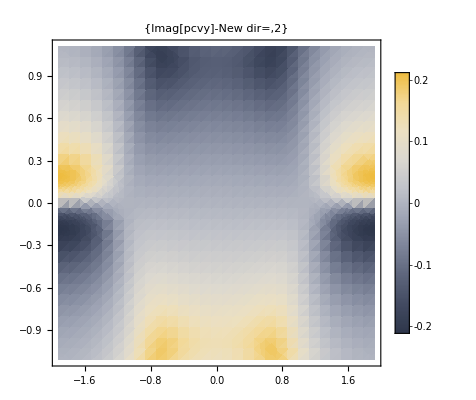

## Momentum matrix element visualization

```mathematica
{
DensityPlot[
Re[ I Eg[kx,ky] cvDipole[kx,ky][[xdir]] ]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"Real pcv dir= ", xdir," Axis-gauge = ", gauge}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 50
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None
,Epilog->epilogBZ
,TicksStyle->Large ]
,

(*gauge={0,1,0};*)


DensityPlot[
Im[ I Eg[kx,ky] cvDipole[kx,ky][[xdir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"Im pcv =" , xdir , " Axis-gauge = ", gauge}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 50
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None 
,Epilog->epilogBZ
,TicksStyle->Large]
}


{
DensityPlot[
Re[I Eg[kx,ky] cvDipole[kx,ky][[ydir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"Re[pcv] dir= ", ydir," Axis-gauge = ", gauge}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 30
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None
,TicksStyle->Large ]
,
DensityPlot[
Im[I Eg[kx,ky] cvDipole[kx,ky][[ydir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"Imag[pcvy]-New dir=" , ydir}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 30
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None
,TicksStyle->Larger ]
}
```

```mathematica
DensityPlot[
Arg[I Eg[kx,ky] cvDipole[kx,ky][[ydir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"Imag[pcvy]-New dir=" , ydir}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 30
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None
,TicksStyle->Larger ]
```

## Berry Connection visualization

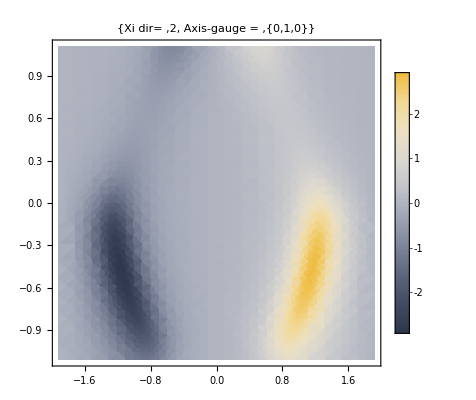
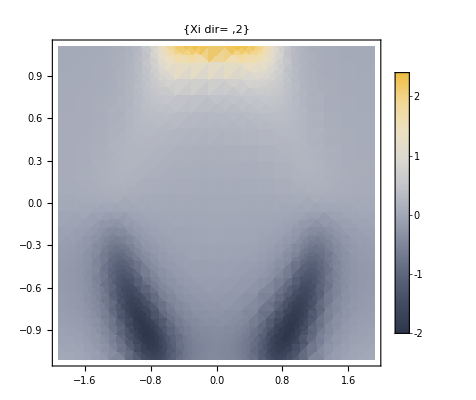

```mathematica
{
DensityPlot[
Re[cBerryConnection[kx,ky][[xdir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"Xi dir= ", ydir," Axis-gauge = ", gauge}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 20
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None
,TicksStyle->Large ]
,
DensityPlot[
Re[cBerryConnection[kx,ky][[ydir]]]
,{kx,kxMin,kxMax}
,{ky,kyMin,kyMax}
,PlotRange -> All
,Frame->True
,FrameStyle->Directive[Black,18]
,PlotLabel-> {"Xi dir= " , ydir}
,ColorFunction-> "GrayYellowTones" 
,PlotPoints-> 20
,ImageSize->size
,PlotLegends-> Automatic
 ,BoxRatios->{1, 1, 1} 
,PlotRangePadding->None
,TicksStyle->Larger ]
}
```

## Testing Laser field

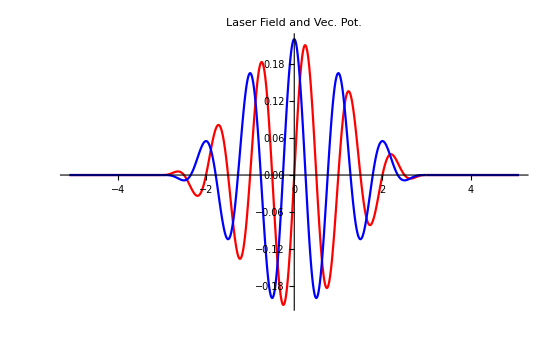

```mathematica
(* Laser parameters *)
w0=0.014; (*laser freq.*)
e0 = 0.003; (*laser field amplitude*)
T0= 2 Pi/w0; (*laser cycle or period*)
Ncycles = 6.; (*No. of cycles*)

alpha0 = Ncycles*T0/2.355; (*time width*)
tmax = 2alpha0;
tmin0=-tmax;
CosWidth=Ncycles*T0;

Plot[{
Ef[t*T0]/w0
,Af[t*T0]
}
,{t,-tmax/T0,tmax/T0}
,PlotRange->All,
PlotStyle->{Red,Blue}
,ImageSize->550
,PlotLabel->"Laser Field and Vec. Pot."
]

regular = 10^-10; 
(*Regularization of Dipole*)
(* xdirection dir =1, ydirection dir=2 *)

dir = 1;
```

```mathematica
{Ef[tmin0 ],Af[tmin0]}
```

{0.,0.}

## Energy Band Gap

```mathematica
(***********************)
(*Max and Min gap*)
dkx1=2kxMax/50;
dky1=2kyMax/40;

(*ϕ=1.16;*)
(*ϕ=0.06;*)
Nphi=1;
aphi={};
aEg={};
aCN={};
i=0;
(*ϕ=i * Pi/(Nphi-0);*)

Tac = Table[Ec[kx,ky]
,{kx,kxMin,kxMax,dkx1}
,{ky,kyMin,kyMax,dky1}
];

Tav = Table[Ev[kx,ky]
,{kx,kxMin,kxMax,dkx1}
,{ky,kyMin,kyMax,dky1}
];


CN=CherNo ;

gap=Min[Tac-Tav];

AppendTo[aphi,ϕ];
AppendTo[aEg,gap];
AppendTo[aCN,CN];
EgMax= Max[Tac-Tav];

Print["\n\nM/t2 = ",M/t2,";  t2/t1 = ",t2/t1, ";\nt1= ",t1*efac, " eV; t2= ",t2*efac," eV;\nM= ",M*efac," eV; phi0= ",ϕ, " rad."];

Print["\ni= ",i,";   Band-Gap= ",gap,";   Max Gap=",EgMax," eV",";  phi0 = ",N[ϕ ,4], "; CNum = ",N[CN,4]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.28584×10^-17+0. ⅈ and 8.68313×10^-11 for the integral and error estimates.

M/t2 = 2.54;  t2/t1 = 0.3333333333333333333333333;
t1= 2.04 eV; t2= 0.68 eV;
M= 1.7272 eV; phi0= 0. rad.

i= 0;   Band-Gap= 0.127454;   Max Gap=0.467578 eV;  phi0 = 0.; CNum = 1.15958×10^-17

## Construction of the momentum matrix elements

```mathematica
xMomentumMatrix := Function[{kx,ky},
{{vGroupVel[kx,ky][[xdir]]+kx , I Eg[kx,ky] cvDipole[kx,ky][[xdir]] },
{-I Eg[kx,ky] vcDipole[kx,ky][[xdir]],cGroupVel[kx,ky][[xdir]]+kx }}
];

ydir=2;
yMomentumMatrix := Function[{kx,ky},
{{vGroupVel[kx,ky][[ydir]]+ky , I Eg[kx,ky] cvDipole[kx,ky][[ydir]] },
{-I Eg[kx,ky] vcDipole[kx,ky][[ydir]],cGroupVel[kx,ky][[ydir]]+ky }}
];


xyMomentumMatrix := Function[{kx,ky},
Conjugate[xMomentumMatrix[kx,ky]].yMomentumMatrix[kx,ky] -Conjugate[yMomentumMatrix[kx,ky]].xMomentumMatrix[kx,ky] 
]
```

$Aborted

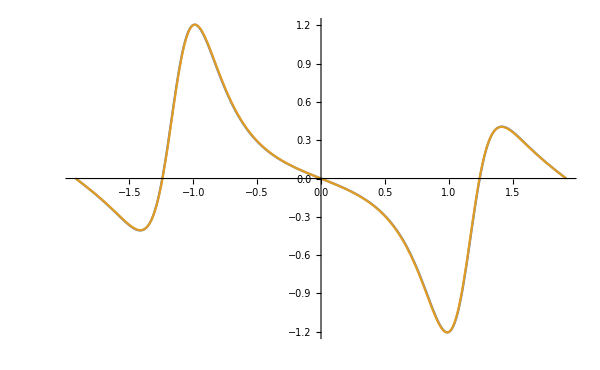

```mathematica
gauge={0,1,0};
kyint1=-0.40;
kyint2=-0.425;
kyint3=-0.43;
kyint4=-0.45;
kyint5=-0.455;
Plot[{(*Im[cvDipole[kx,kyint1][[1]]],*)
Im[cvDipole[kx,kyint2][[1]]]
,Im[cvDipole[kx,kyint3][[1]]]
(*,Im[cvDipole[kx,kyint4][[1]]]
,Im[cvDipole[kx,kyint5][[1]]]*)}
,{kx,kxMin,kxMax}
,PlotRange->All,ImageSize->600,TicksStyle->Large]
```

## Chern Number

```mathematica
(********************************)
(*Calculation of the CHERN No.*)
CherNo
```

## Time Axis and more parameters

{0.,0.}

dt = 0.75
Ntime = 2494
 kyint = 0

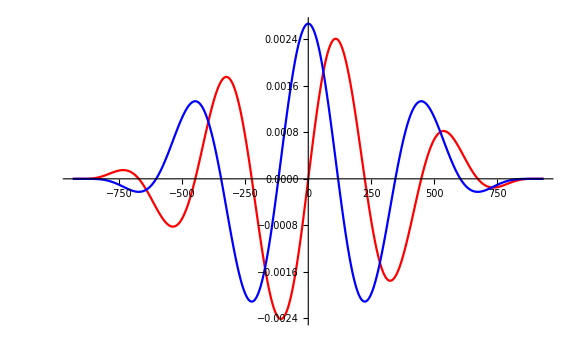

```mathematica
(* Laser parameters *)
w0=0.014; (*laser freq.*)
e0 = 0.0025; (*laser field amplitude*)


T0= 2. Pi/w0; (*laser cycle or period*)
dt=0.75;(*T00/160.06/2*) (*Time step*)


Ncycles = 4.; (*No. of cycles*)

(*alpha0 = Ncycles*T0/2.355; (*time width or integration window*)
tmax = 5. alpha0;*)
(*tmin=-tmax;
tmin0=tmin;
*)


CosWidth= Ncycles*T0;
tmax=CosWidth*.521;


tmin=-tmax;
tmin0=tmin;

Ntime = Floor[2 tmax/dt];
If[ Mod[Ntime,2]!= 0,
Ntime=Ntime+1
];




(*Numerical time axis for time evolution of SBEs*)
tme= timeaxes[dt,Ntime];
time=tme[[]][[1]];
freq = tme[[]][[2]]; 

T2 = 220; (*Dephasing*)

(* some Momentum parameters *)
xdir = 1;
ydir=  2;
kxMax0 = kxMax; (*Max grid space momentum *)
kyint=0;
{Ef[tmin0],Af[tmin0]}

Print["\ndt = ",N[dt,4], "\nNtime = ",Ntime,"\n kyint = ",kyint];


EfieldN = Table[{time[[i]],Ef[ time[[i]] ]},{i,1,Ntime}];
AfieldN = Table[{time[[i]],Af[ time[[i]] ]* w0},{i,1,Ntime}];
ListLinePlot[{EfieldN,AfieldN},PlotRange->All,PlotStyle->{Red,Blue},ImageSize->Large]
```

```mathematica
gauge
```

{0,1,0}

## Momentum axis, derivative operator, Rabbi Frequency, etc

```mathematica
(*Momentum Axis*)
Nkx= 31; (*30*)

kxx = momaxis[Nkx,kxMin]; (*momentum space axis*)
dkx = kxx[[2]]-kxx[[1]];(*2 kxMax/(Nkx-1); *)(*Momentum space step => momentum step*)
kxx0=kxx;



(*Rabbi Freq. *)
ROmega := Function[

{kx,ky,t}

,Ef[t]*
cvDipole[ kx, ky][[xdir]] 

];



ConjROmega := Function[

{kx,ky,t}

,Ef[t]*vcDipole[ kx, ky][[xdir]] 

];


(*Stability condition*)
CFL=e0 dt/dkx ;
Print["\nCFL = ",CFL];


MaskFunc := Function[{t,ta,tb,al,om,dat },
Ntime=Length[t];

Table[

taux=t[[j]];

If[taux≤ ta, 

Exp[-2(taux-ta)^2 /(al*al)]*dat[[j]]
,

If[taux≤  tb,
dat[[j]],
Exp[-2(taux-tb)^2 /(om*om)]*dat[[j]]
]

]

,{j,1,Ntime}
]

];
```

CFL = 0.0146561

## Dynamical evolution of populations and SBEs defined by Eqs 1 -- 3, according to the constriction

```mathematica
Fehlbergamat={{1/4},{3/32,9/32},{1932/2197,-7200/2197,7296/2197},{439/216,-8,3680/513,-845/4104},{-8/27,2,-3544/2565,1859/4104,-11/40}};Fehlbergbvec={25/216,0,1408/2565,2197/4104,-1/5,0};Fehlbergcvec={1/4,3/8,12/13,1,1/2};Fehlbergevec={-1/360,0,128/4275,2197/75240,-1/50,-2/55};FehlbergCoefficients[4,p_]:=N[{Fehlbergamat,Fehlbergbvec,Fehlbergcvec,Fehlbergevec},p];


DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
(*  STATIC FRAME LENGTH GAUGE, LG *)
Clear[solverLG,t];
(*ϕ=0.06;*)


solverLG=

NDSolve[
(*ParametricNDSolve[*)
{

(*******************************************)
(****     Evol. Equations of SBEs       ****)
(*******************************************)
(*Equation1*)
D[pi[kx,t],t]  -Ef[t]D[pi[kx,t],kx]== 
-I(
 Eg[kx,kyint] 

+2. Ef[t] * cBerryConnection[kx,kyint][[xdir]]

(*-  I/T2*)
)* pi[kx,t] 

- I *ROmega[kx,kyint,t] *(1. -2.*nc[kx,t])



(*Equation2*)
,D[nc[kx,t],t] -Ef[t]D[nc[kx,t],kx]== -2*Im[ ConjROmega[kx,kyint,t]* pi[kx,t] ]
(*******************************************)


(*******************************************)
(****             Initials             ****)
(*******************************************)
(*Initials1*)
,pi[kxMin,t]==pi[kxMax,t]
,pi[kx,tmin]==0.

(*Initials2*)
,nc[kxMin,t]==nc[kxMax,t]
,nc[kx,tmin]==0.
(*******************************************)

}

,{pi,nc}

,{kx,kxMin,kxMax}

,{t,tmin,tmax}

(*,Method->"ImplicitRungeKutta",*)
(*,Method-> RK5*)
(*,{kx,ky}*)

,AccuracyGoal->10,PrecisionGoal->10

,MaxStepSize->{dkx,dt}
                            
 (*,Method->{"ExplicitRungeKutta"
,"DifferenceOrder"->5
,"Coefficients"->DOPRICoefficients
,"StiffnessTest"->False}*)

];
```

### Testing solution at K’ point;

```mathematica
kx1=K1[[1]]
ky1=0;
ktime=1;

solLGSF=solverLG;
{lgTickTime, trash}=Re[         

 Evaluate[         pi[ kx1, time[[ktime]]    ]/.solLGSF    ]   
   
]//AbsoluteTiming
```

-1.27933315157320165728569

{0.00005,{0.}}

{934.4529871312672701491216,7.1331×10^-8}

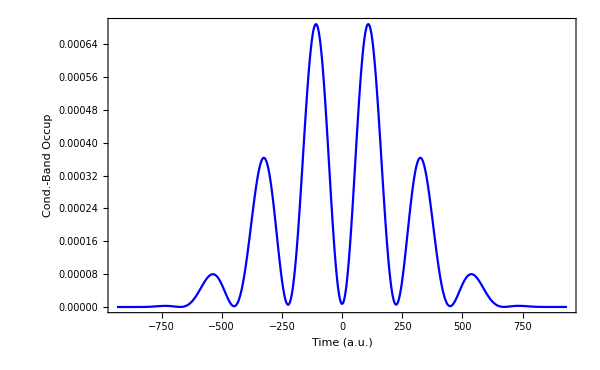

```mathematica
(* **** NUMERICAL TEST OF SOLVER LG & SF **** *)

(* Occ. LG EVALUATION *)
ncSol1SF=Table[ 

Clear[solLGSF];

kx1=kxx[[i]];


solLGSF=solverLG;

Table[
temp=Re[Evaluate[nc[kx1,time[[ktime]]]/.solLGSF]]*dkx;

temp[[1]]

,{ktime,Ntime}
]

,{i,1,Nkx}

];

(* Mom integral of Occ. LG EVALUATION *)
ncSolLGSF=Table[
 
temp0=0.;

Table[
temp0=temp0+ncSol1SF[[i,ktime]]
,{i,1,Nkx}
];

{time[[ktime]],temp0}

,

{ktime,1,Ntime} 

];
ncSolLGSF[[Ntime]]

ListLinePlot[ncSolLGSF,PlotRange->All, ImageSize->600,PlotStyle->{Red,Blue}
(*,ScalingFunctions->"Log"*), Frame->True, FrameLabel-> {"Time (a.u.)","Cond.-Band Occup"}]
```

```mathematica
(* Coherent LG EVALUATION *)
solLGSF=solverLG;
piSol1SF=Table[ 

(*Clear[solLGSF];*)

kx1=kxx[[i]];

Table[

time1=time[[ktime]] ;

temp=  ( pi[kx1,  time1 ]/.solLGSF   ) *dkx;

temp[[1]]

,{ktime,1,Ntime}
]

,{i,1,Nkx}

];
```

## Moving Frame MF implementation

```mathematica
(************************************)
(*  Moving FRAME LENGTH GAUGE, LG *)
Clear[solverMFLG,t];
(*ϕ=0.06;*)
(*gauge={0,1,0};*)
(*kyint=-0.4;*)

solverMFLG= Function[kx,

NDSolve[
(*
ParametricNDSolve[
*)

{

(*******************************************)
(****     Evol. Equations of SBEs       ****)
(*******************************************)
(*Equation1*)
D[pi[t],t]  == 
-I(
 Eg[kx+Af[t],kyint] 

+2. Ef[t] * cBerryConnection[kx+Af[t],kyint][[xdir]]

(*-  I/T2*)
)* pi[t] 

- I *ROmega[kx+Af[t],kyint,t] *(1. -2.*nc[t])



(*Equation2*)
,D[nc[t],t] == -2*Im[ ConjROmega[kx+Af[t],kyint,t]* pi[t] ]
(*******************************************)


(*******************************************)
(****             Initials             ****)
(*******************************************)
(*Initials1*)
(*,pi[kxMin,t]==pi[kxMax,t]*)
,pi[tmin]==0.

(*Initials2*)
(*,nc[kxMin,t]==nc[kxMax,t]*)
,nc[tmin]==0.
(*******************************************)

}

,{pi,nc}

(*,{kx,kxMin,kxMax}*)

,{t,tmin,tmax}

(*,Method->"ImplicitRungeKutta",*)
(*,Method-> RK5*)

(*,{kx,ky}*)
,AccuracyGoal->10,PrecisionGoal->10

,MaxStepSize->dt
                            
 (*,Method->{
"ExplicitRungeKutta"
,"DifferenceOrder"->5
,"Coefficients"->DOPRICoefficients
,"StiffnessTest"->False
}*)

]

];
```

## NUMERICAL TEST OF SOLVER LG -MF

```mathematica
(* **** NUMERICAL TEST OF SOLVER LG -MF **** *)
kx1=K1[[1]]+0dk/4.;
ky1=0;
ktime=1;

solLGMF=solverMFLG[kx1];
{lgTickTime, trash}=Re[         

 Evaluate[         nc[  time[[ktime]]    ]/.solLGMF    ]   
   
]//AbsoluteTiming
```

{0.001016,{0.}}

```mathematica
(***************************)
(* Occ. LG EVALUATION MF *)
ncSol1MF=Table[ 

Clear[solLGMF];

kx1=kxx[[i]];

solLGMF=solverMFLG[kx1];

Table[
temp=Re[Evaluate[nc[time[[ktime]]]/.solLGMF]]*dkx;

temp[[1]]

,{ktime,Ntime}
]

,{i,1,Nkx}

];
```

```mathematica
(* Coherent LG EVALUATION -- MF *)
piSol1MF=Table[ 

Clear[solLGMF];

kx1=kxx[[i]];


solLGMF=solverMFLG[kx1];

Table[
temp=Evaluate[pi[time[[ktime]]]/.solLGMF]*dkx;

temp[[1]]

,{ktime,Ntime}
]

,{i,1,Nkx}

];
```

{934.4529871312672701491216,3.43093×10^-9}

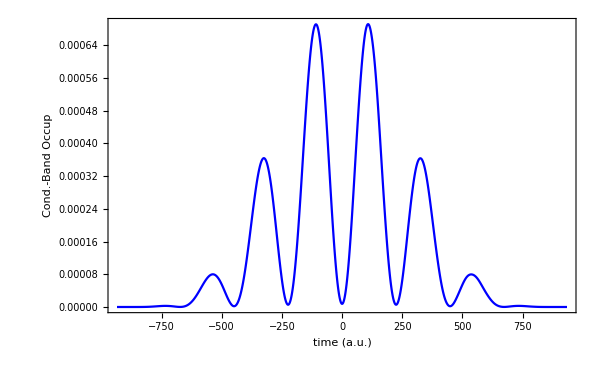

```mathematica
(* Mom integral of Occ. LG EVALUATION *)
ncSolLGMF=Table[
 
temp0=0.;

Table[

temp0=temp0+ncSol1MF[[i,ktime]]

,{i,1,Nkx}

];

{time[[ktime]],temp0},

{ktime,1,Ntime} 
];

ncSolLGMF[[Ntime]]
ListLinePlot[ncSolLGMF,PlotRange->All, ImageSize->600,PlotStyle->{Red,Blue}, Frame->True, FrameLabel-> {"time (a.u.)","Cond.-Band Occup"},PlotLegends->"MF-LG"(*,ScalingFunctions->"Log"*)]
```

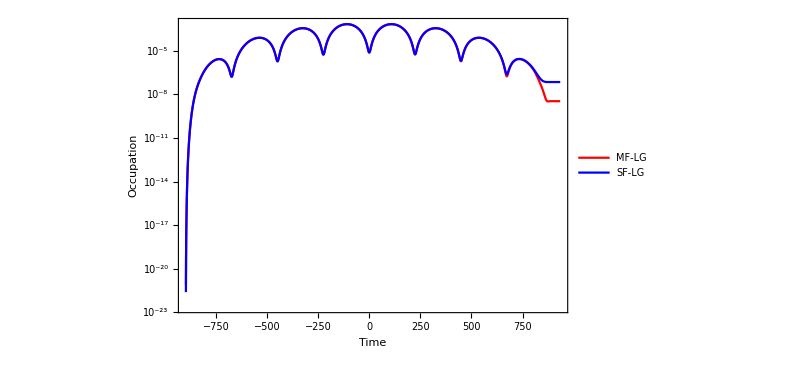

```mathematica
ListLinePlot[{ncSolLGMF,ncSolLGSF},PlotRange->All, ImageSize->600,PlotStyle->{Red,Blue},ScalingFunctions->"Log",Frame->True,FrameLabel->{"Time","Occupation"},PlotLegends->{"MF-LG","SF-LG"}]
```

## Numerical implementation of the Velocity Gauge (VG)

```mathematica
(*  velocity *)
Clear[solverVG,t];
(*ϕ=0.06;*)

solverVG:= Function[kx,

NDSolve[
(*ParametricNDSolve[*)
{

(*******************************************)
(****     Evol. Equations of SBEs  VG     ****)
(*******************************************)
(*Equation1*)
D[pi[t],t]  == 
-I(
 Eg[kx,kyint] 

+Af[t] * (cGroupVel[kx,kyint][[xdir]] - vGroupVel[kx,kyint][[xdir]])

(*-  I/T2*)
)* pi[t] 

+Af[t]* Eg[kx,kyint]cvDipole[kx,kyint][[xdir]] *(1. -2.*nc[t])



(*Equation2*)
,D[nc[t],t] == 2Af[t]*Im[ I*Eg[kx,kyint]*vcDipole[kx,kyint][[xdir]]* pi[t] ]
(*******************************************)


(*******************************************)
(****             Initials             ****)
(*******************************************)
(*Initials1*)
(*,pi[kxMin,t]==pi[kxMax,t]*)
,pi[tmin]==0.

(*Initials2*)
(*,nc[kxMin,t]==nc[kxMax,t]*)
,nc[tmin]==0.
(*******************************************)

}

,{pi,nc}

(*,{kx,kxMin,kxMax}*)

,{t,tmin,tmax}

(*,Method->"ImplicitRungeKutta",*)
(*,Method-> RK5*)

(*,{kx,ky}*)
,AccuracyGoal->10,PrecisionGoal->10

,MaxStepSize->dt
                            
(*,Method->{"ExplicitRungeKutta"
,"DifferenceOrder"->5
,"Coefficients"->DOPRICoefficients
,"StiffnessTest"->False}*)

]

];
```

```mathematica
(* **** NUMERICAL TEST OF SOLVER VG  **** *)
kx1=K1[[1]]+0dkx/2.;
ky1=0;
ktime=1;

solVG=solverVG[kx1];         
temp=nc[  time[[ktime]]    ]/.solVG;    (*//  AbsoluteTiming*)
{kx1,temp[[1]]}
```

{-1.27933,0.+0. ⅈ}

```mathematica
(***********************************
OCCUPATION OF CONDUCTION BAND VG*)
ncSol2=Table[ 

kx1=kxx[[i]];

Clear[solVG,t];

solVG=solverVG[kx1];

Table[

time1=time[[ktime]];

temp=Re[Evaluate[   nc[  time1  ]/.solVG  ]]   *dkx;

temp[[1]]

,{ktime,1,Ntime}

]
,{i,1,Nkx}

];
```

```mathematica
(*EVALUATING COHERENT IN VG*)
piSol2=Table[ 

kx1=kxx[[i]];
Clear[solVG,t];

solVG=solverVG[kx1];

Table[
time1=time[[ktime]];

temp=Evaluate[   pi[  time1  ]/.solVG  ]   *dkx;
temp[[1]]

,{ktime,1,Ntime}

]
,{i,1,Nkx}

];
```

```mathematica
(* OCCUPATION INTEGRAL on MOMENTUM, VG  *)
ncSolVG=Table[
 
temp0=0.;

Table[temp0=temp0+ncSol2[[i,ktime]],{i,1,Nkx}];


{time[[ktime]],temp0}

,{ktime,1,Ntime} 

];
ncSolVG//Dimensions
```

{2494,2}

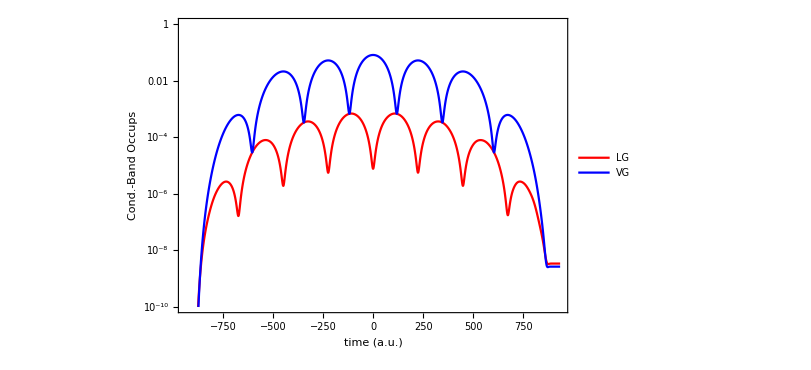

```mathematica
ListLinePlot[{ncSolLGMF,ncSolVG},PlotRange->{{tmin0,tmax},{1 10^-10,1 10^0}}, ImageSize->600,PlotStyle->{Red,Blue},TicksStyle->Large,PlotLegends->{"LG","VG"},ScalingFunctions->"Log", Frame->True, FrameLabel-> {"time (a.u.)","Cond.-Band Occups"}]
```

## Visualizing final momentum distribution of the occupation nc

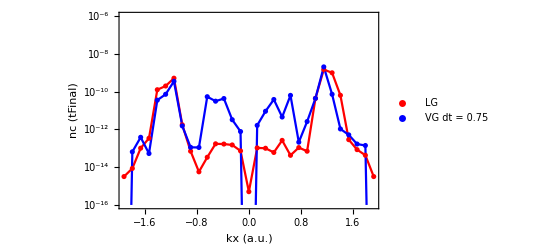
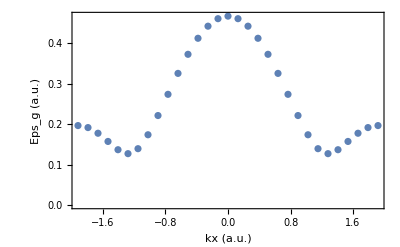

```mathematica
ncSol11LG=Table[{kxx[[i]],Abs[ncSol1MF[[i,Ntime]]]},{i,1,Nkx}];
ncSol22VG=Table[{kxx[[i]],Abs[ncSol2[[i,Ntime]]]},{i,1,Nkx}];
EnergyDiff = Table[{kxx[[i]],Eg[kxx[[i]],kyint]},{i,1,Nkx}];


{ListPlot[{ncSol11LG,ncSol22VG,ncSol11LG,ncSol22VG}
,PlotRange->{All,{10^-16,10^-6}}
, ImageSize->400
,PlotStyle->{Red,Blue,Red,Blue}
,Joined->{False,False,True,True}
,TicksStyle->Large
,PlotLegends->{"LG","VG dt = "<>ToString[N[dt,2]] }
,ScalingFunctions->"Log",Frame->True
,FrameLabel-> {"kx (a.u.)","nc (tFinal)"}]
,
ListPlot[EnergyDiff,PlotRange->All,ImageSize->400
,TicksStyle->Large,Frame->True,
FrameLabel-> {"kx (a.u.)","Eps_g (a.u.)"}]}
```

## Computing Currents for both LG (MF)

```mathematica
(*VARIABLES FOR CALCULATION CURRENTS*)
JxVGer= Table[0,{i,1,Floor[Ntime]}];
JxLGer= Table[0,{i,1,Floor[Ntime]}];

JxVGra= Table[0,{i,1,Floor[Ntime]}];
JxLGra= Table[0,{i,1,Floor[Ntime]}];

JxLGMFra= Table[0,{i,1,Floor[Ntime]}];
```

```mathematica
(****  Evaluation of re-combination dipole and matrix element ****)

(* DIPOLE MATRIX ELEMENT *)
xvcdip = Table[ 

xktemp=kxx[[i]];

 vcDipole[ xktemp, kyint][[xdir]] 
,{i,1,Nkx}

];

(*MOMENTUM MATRIX ELEMENT *)
xvcP = Table[ 

xktemp=kxx[[i]];

-I vcDipole[ xktemp, kyint][[xdir]] *Eg[kxx[[i]],kyint  ]
,{i,1,Nkx}

];

(*** GROUP VELOCITY VAL. BAND ***)	
xvvel0= Table[ 

xktemp=kxx[[i]];
 
vGroupVel[xktemp,kyint][[xdir]]

,{i,1,Nkx}

];


(*** GROUP VELOCITY CON. BAND ***)	
xcvel0= Table[ 

xktemp=kxx[[i]];

cGroupVel[xktemp,kyint][[xdir]]

,{i,1,Nkx}

];
```

```mathematica
(* *** Inter-intra EXPECTATION VALUES: LG CURRENTS via SF *** *)
ktemp=1;

Do[  

temp=Sum[ 

2 Re[ piSol1SF[[i,ktime]]*  xvcdip[[i]] ]

,{i,1,Nkx} 

];


JxLGer[[ktemp]]=temp;


(*

 *
*
*

*)


temp=Sum[ 
 ncSol1SF[[i,ktime] ]* xcvel0[[i]] +(dkx-ncSol1SF[[i,ktime]]) * xvvel0[[i]] 
,{i,1,Nkx} 
];


JxLGra[[ktemp]]=temp;


ktemp=ktemp+1;

,{ktime,1,Ntime}

];
```

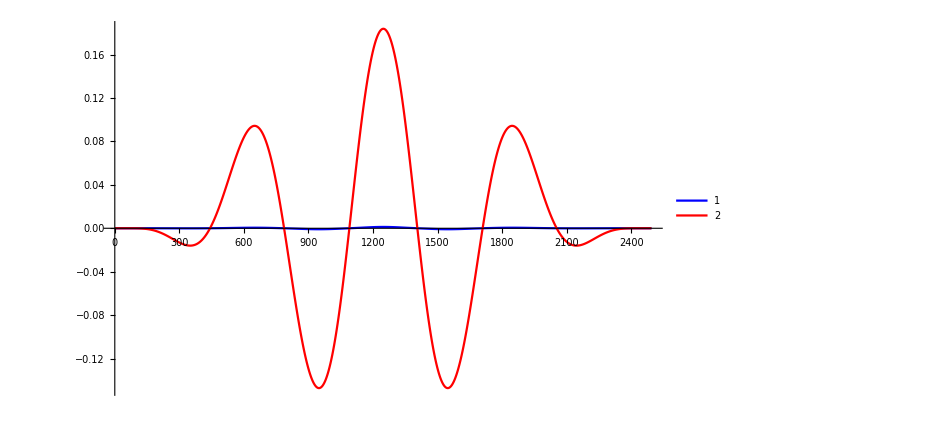

```mathematica
ListPlot[{1(JxLGra-JxLGra[[1]])
,JxVGra-JxVGra[[1]]}
,PlotRange->{All,All}
,Joined->True
,PlotStyle->{Blue,Red},ImageSize->700,PlotLegends->Automatic]
```

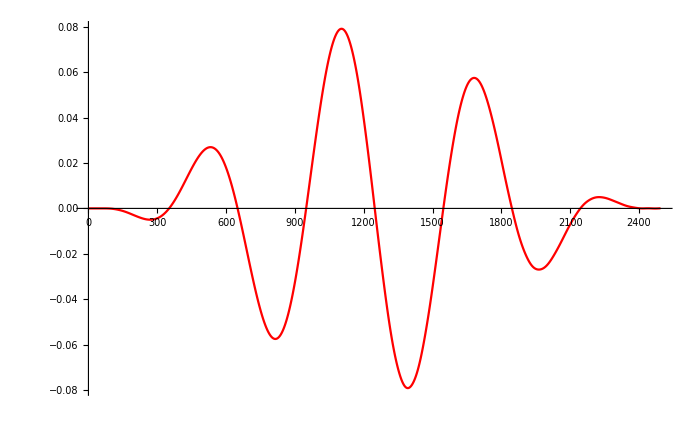

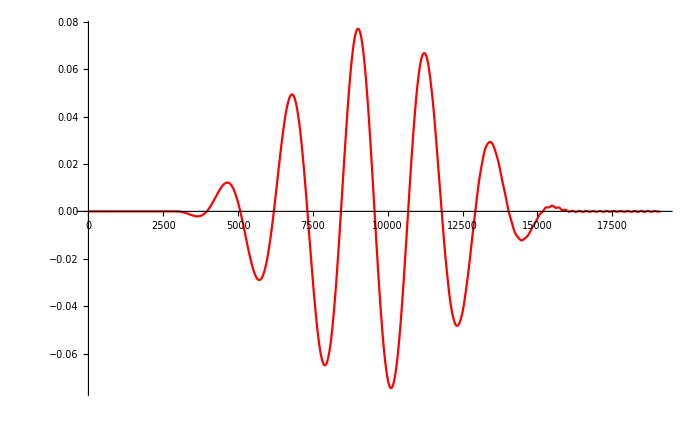

```mathematica
(*** INTRA BAND CURRENT VIA MF PICTURE ON LG  ***)

JxLGra=Table[

temp=Sum[ 

xcvel1 = cGroupVel[kxx[[i]]+Af[time[[ktime]]],kyint][[xdir]];
xvvel1 = vGroupVel[kxx[[i]]+Af[time[[ktime]]],kyint][[xdir]];

 ncSol1MF[[i,ktime] ]* xcvel1 +(dkx-ncSol1MF[[i,ktime]]) * xvvel1

,{i,1,Nkx} 

]

,{ktime,1,Ntime}

];



(* *** Inter-intra EXPECTATION VALUES: LG CURRENTS via MF *** *)
ktemp=1;

Do[  

temp=Sum[ 

  xktemp     =kxx[[i]]+Af[ time[[ktime]] ];
  xvcdip0 =vcDipole[ xktemp, kyint][[xdir]] ;

2 Re[ piSol1MF[[i,ktime]]*  xvcdip0 ]

,{i,1,Nkx} 

];


JxLGer[[ktime]]=temp;

,{ktime,1,Ntime}
]

ListPlot[JxLGer
,PlotRange->{All,All}
,Joined->True
,PlotStyle->{Blue,Red},ImageSize->700]
```

```mathematica
(* *** INTER-INTRA BAND RADIATION VG *** *)
ktemp=1;

Do[  


temp=Sum[ 

2 Re[ piSol2[[i,ktime]]* xvcdip[[i]](**xvcP[[i]] *)  ]

,{i,1,Nkx} 

];


JxVGer[[ktemp]]=temp;


temp=Sum[ 
ncSol2[[i,ktime] ]* (xcvel0[[i]]+kxx[[i]]) +(dkx-ncSol2[[i,ktime]]) * (xvvel0[[i]]+kxx[[i]] )
,{i,1,Nkx} 
];

JxVGra[[ktemp]]=temp+ Af[  time[[ktime]] ] ;

ktemp=ktemp+1;

,{ktime,1,Ntime}

];
```

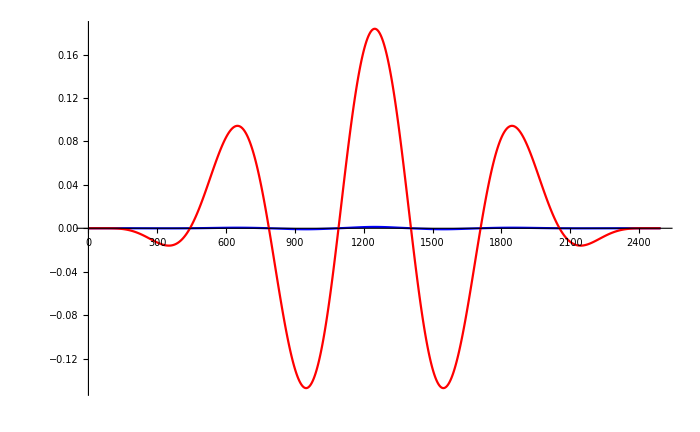

```mathematica
ListPlot[{(JxLGra-JxLGra[[1]]),JxVGra-JxVGra[[1]]}
,PlotRange->{All,All}
,Joined->True
,PlotStyle->{Blue,Red},ImageSize->700]

ListPlot[{(JxLGra-JxLGra[[1]]),JxVGer-JxVGer[[1]]}
,PlotRange->{All,All}
,Joined->True
,PlotStyle->{Blue,Red},ImageSize->700]
```

## CALCULATION OF THE HHG SPECTRUM VIA LG AND VG

```mathematica
(*** CALCULATION OF THE HHG SPECTRUM VIA LG AND VG ***)


black=Table[BlackmanWindow[  time[[i]]/(time[[Ntime]] -time[[1]] ) ],{i,1,Ntime}];
(*JxVGer0 =JxVGer;*)
JxVGer0 = Table[ 

If[ktime>1 && ktime < Ntime,

(JxVGer[[ktime+1]]-JxVGer[[ktime-1]])/2./dt
,
0
]

,{ktime,1,Ntime}

];


aJxVGer = Table[ 

If[ktime>1 && ktime < Ntime,

(JxVGer0[[ktime+1]]-JxVGer0[[ktime-1]])/2./dt
,
0
]

,{ktime,1,Ntime}

];

aJxVGra  = Table[ 

If[ktime>1 && ktime < Ntime,

(JxVGra[[ktime+1]]-JxVGra[[ktime-1]])/2./dt
,
0
]

,{ktime,1,Ntime}

];


JxVGra1=Table[black[[i]]*(aJxVGra[[i]]-aJxVGra[[1]]),{i,1,Ntime}];
JxVGer1=Table[black[[i]]*aJxVGer[[i]],{i,1,Ntime}];


JxLGra1=Table[black[[i]]*(JxLGra[[i]]-JxLGra[[1]]),{i,1,Ntime}];
JxLGer1=Table[black[[i]]*JxLGer[[i]],{i,1,Ntime}];
```

## HHG Spectrum

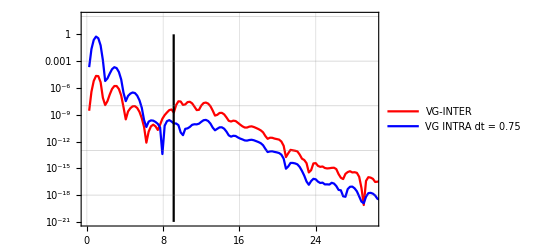

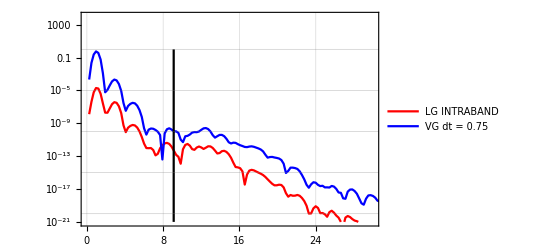
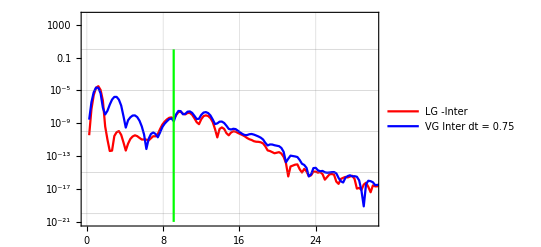

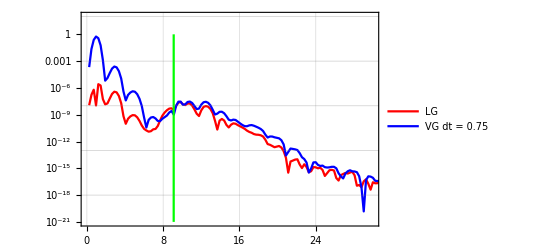

```mathematica
ssf=RotateRight[freq,Ntime/2];
ssf//Dimensions;
isize=400;
(*jraL0=Fourier[JxLGra1]*dt *Sqrt[Ntime];*)


jraV0=Fourier[JxVGra1]*dt *Sqrt[Ntime];
jerV0 =Fourier[JxVGer1]*dt *Sqrt[Ntime];

jVGtot0=Table[Abs[ jraV0[[ktime]] -jerV0[[ktime]] ] ,{ktime,1,Ntime}] ;
jVGtot=Table[{ssf[[i]]/w0,jVGtot0[[i]]^2},{i,2,Ntime/2}];

jraV1=Table[{ssf[[i]]/w0,Abs[jraV0[[i]]]^2},{i,2,Ntime/2}];
jerV1=Table[{ssf[[i]]/w0,Abs[jerV0[[i]]]^2},{i,2,Ntime/2}];

ListPlot[{jerV1,jraV1,Table[{gap/w0,10^-i},{i,0,21}]}
,PlotRange->{{0,30},{10^-21,10^2}}
, ImageSize->isize
,PlotStyle->{Red,Blue,Black,Blue}
,Joined-> True(*{False,False,True,True}*)
,TicksStyle->Large
,PlotLegends->{"VG-INTER" <> "  ","VG INTRA dt = "<>ToString[N[dt,2]] }
,ScalingFunctions->"Log"
,Frame->True
,GridLines->Automatic
,PlotLegends->{"Harmonic Order","Yield"}]


tempFT0=Fourier[JxLGer1] *Sqrt[Ntime] *dt;
tempFT1 = Table[tempFT0[[ktime]]*ssf[[ktime]]*ssf[[ktime]]*I*I,{ktime,1,Ntime}]; 

tempFT0 = Fourier[JxLGra1]*Sqrt[Ntime] *dt;
tempFT2 = Table[ -tempFT0[[ktime]]*ssf[[ktime]]*I,{ktime,1,Ntime}]; 
jraL0=tempFT0;

jLGtot0=Abs[ tempFT1 +tempFT2 ] ;
jLGtot=Table[{ssf[[i]]/w0,jLGtot0[[i]]^2},{i,2,Ntime/2}];



jerL0=Abs[Fourier[JxLGer1]]*dt*Sqrt[Ntime];
jerV0=Abs[Fourier[JxVGer1]]*dt*Sqrt[Ntime];


jraL1=Table[{ssf[[i]]/w0,ssf[[i]]^2Abs[jraL0[[i]]]^2},{i,2,Ntime/2}];
jerL1=Table[{ssf[[i]]/w0,ssf[[i]]^4 Abs[jerL0[[i]]]^2},{i,2,Ntime/2}];



{
(*INTRABAND*)
ListPlot[{jraL1,jraV1,Table[{gap/w0,10^-i},{i,0,21}]}
,PlotRange->{{0,30},{10^-21,10^4}}, ImageSize->isize
,PlotStyle->{Red,Blue,Black,Blue},Joined-> True(*{False,False,True,True}*)
,TicksStyle->Large
,PlotLegends->{"LG" <> "  INTRABAND","VG dt = "<>ToString[N[dt,2]] }
,ScalingFunctions->"Log",Frame->True,GridLines->Automatic,PlotLegends->{"Harmonic Order","Yield"}],

(*** INTERBAND ***)
ListPlot[{jerL1,jerV1,Table[{gap/w0,10^-i},{i,0,21}]},PlotRange->{{0,30},{10^-21,10^4}}
, ImageSize->isize
,PlotStyle->{Red,Blue,Green,Black}
,Joined-> True(*{False,False,True,True}*),TicksStyle->Large
,PlotLegends->{"LG -Inter" <> "","VG Inter dt = "<>ToString[N[dt,2]] }
,ScalingFunctions->"Log",Frame->True,GridLines->Automatic,PlotLegends->{"Harmonic Order","Yield"}]
}


(*** TOTAL HHG FOR LG vs VG ***)
ListPlot[{jLGtot,jVGtot,Table[{gap/w0,10^-i},{i,0,21}]}
,PlotRange->{{0,30},{10^-21,10^2}}
, ImageSize->isize
,PlotStyle->{Red,Blue,Green,Black}
,Joined-> True(*{False,False,True,True}*)
,TicksStyle->Large
,PlotLegends->{"LG" <> "  ","VG dt = "<>ToString[N[dt,2]] }
,ScalingFunctions->"Log"
,Frame->True,GridLines->Automatic,PlotLegends->{"Harmonic Order","Yield"}]
```

## Importing Data from SBEs-C++ code

```mathematica
(*PathSpectrumLG="/Users/achacon/antelope/src/SBE_HaldaneModel4/test1D0/HHG__CNo-0.1__E0index__0000__.dat";
JintraP="/Users/achacon/antelope/src/SBE_HaldaneModel4/test1D/intraband_current_full_evol.dat";
JinterP="/Users/achacon/antelope/src/SBE_HaldaneModel4/test1D/interband_dipole_full_evol.dat";
LGtimeP="/Users/achacon/antelope/src/SBE_HaldaneModel4/test1D/outlaserdata.dat";


LGMFSpectrum=Import[PathSpectrumLG,"Data"];
Jintra=Import[JintraP,"Data"];
Jinter=Import[JinterP,"Data"];
LGTime=Import[LGtimeP,"Data"];

LGMFSpectrum2=Table[{LGMFSpectrum[[i,1]],Power[10.,LGMFSpectrum[[i,2]]]},{i,1,Length[LGMFSpectrum[[All,1]]]}];

*)
```